Analyze statistics output by Noisy Compiler

psm@mit.edu

```mathematica
SetDirectory[NotebookDirectory[]];

prefixColumn[statistics_, prefix_, column_]:=Total[#[[column]]&/@ Select[statistics, StringMatchQ[#[[2]], prefix<>"*"]&]];



doPlot[title_,rawLabels_, data_] := Module[{piePlot, barPlot, labels},
(* Rewrite "skank" to "sk" for plotting *)
labels = StringReplace[#,"skank"->"sk"]&/@rawLabels;

piePlot = PieChart[data,
ChartLabels->Placed[ Style[#, FontSize->14, Gray]&/@labels,"VerticalCallout"],
SectorOrigin->{Automatic,1},
PlotLabel->title,
Ticks->None,
ChartStyle-> 16,
ChartStyle-> Directive["AvocadoColors", FontSize-> 14, FontFamily-> "Helvetica"],
ImageSize->{600,300}, 
ImagePadding->{{150,150} ,{0,0}}];

barPlot = BarChart[{data},
ChartLegends-> MapIndexed[StringReplace[#, "\n"-> " "]&, labels, {1}] , 
ScalingFunctions->"Log",
PlotLabel->title,
PlotTheme-> "Detailed",
(*ChartStyle-> Directive[FontSize-> 15, FontFamily-> "Helvetica"],*) 
FrameStyle-> Directive[FontSize-> 15, FontFamily-> "Helvetica"],
(*ImagePadding->{{50,0} ,{150,150}},*)
ImagePadding->40,
ImageSize->300,
AspectRatio->1/1.5];

GraphicsRow[{piePlot, barPlot}]
];


(*
   TODO: This function may currently be overly sensitive to extraneous newlines.
One way to get around this would be to remove all Null / {} entries, and then
  process the data based on that.
*)
getDataSubsetForTag[data_, tag_] := Module[{startIndex, endIndex},
startIndex = Position[data,tag][[1]][[1]];(*Print[startIndex];*)

endIndex = If[Position[data[[startIndex+2;;]],{}] == {},
			Length[data],
			startIndex + Position[data[[startIndex+2;;]],{}][[1]][[1]] ];(*Print[endIndex];*)

(*Print[data[[startIndex;;endIndex]]];*)

data[[startIndex;;endIndex]]
];

dtraceStatsForFile[filename_, tag_] := Module[{rawFile, dtraceResidencyNanosecondsTable, dtraceResidencyNanosecondsTotal, dtraceResidencyNanosecondsTableNoisySubset, dtraceResidencyNanosecondsNoisySubsetTotal, dtraceResidencyNanosecondsTableNoisySubsetPercentages, dtraceResidencyNanosecondsTableNoisySubsetPercentagesAndRest},


rawFile = Import[filename, "Table"];
If[Length[Position[rawFile,tag]] == 0, Return[{}]];


dtraceResidencyNanosecondsTable = Select[getDataSubsetForTag[rawFile, tag], Length[#]== 2 && NumberQ[#[[2]]]&];
(*Print["dtraceResidencyNanosecondsTable == ", dtraceResidencyNanosecondsTable//TableForm];*)
dtraceResidencyNanosecondsTotal = Total[#[[2]]&/@dtraceResidencyNanosecondsTable];

dtraceResidencyNanosecondsTableNoisySubset = Select[dtraceResidencyNanosecondsTable, (StringMatchQ[#[[1]],"*Noisy*"]||StringMatchQ[#[[1]],"*noisy*"] || StringMatchQ[#[[1]], "*flex*"]||StringMatchQ[#[[1]],"*moveHead*"]||StringMatchQ[#[[1]],"*nextToken*"]|| StringMatchQ[#[[1]], "*skank*"])&];
dtraceResidencyNanosecondsNoisySubsetTotal = Total[#[[2]]&/@dtraceResidencyNanosecondsTableNoisySubset];
dtraceResidencyNanosecondsTableNoisySubsetPercentages = {#[[1]], 100*N[(#[[2]])/dtraceResidencyNanosecondsTotal]}&/@dtraceResidencyNanosecondsTableNoisySubset;
dtraceResidencyNanosecondsTableNoisySubsetPercentagesAndRest = Append[dtraceResidencyNanosecondsTableNoisySubsetPercentages, {"Other",100*N[(dtraceResidencyNanosecondsTotal-dtraceResidencyNanosecondsNoisySubsetTotal)/dtraceResidencyNanosecondsTotal] }];


dtraceResidencyNanosecondsTableNoisySubsetPercentagesAndRest
];


dtraceNoisyOnlyStatsForFile[filename_, tag_] := Module[{rawFile, dtraceResidencyNanosecondsTable, dtraceResidencyNanosecondsTableNoisySubset, dtraceResidencyNanosecondsNoisySubsetTotal, dtraceResidencyNanosecondsTableNoisySubsetPercentages},


rawFile = Import[filename, "Table"];
If[Length[Position[rawFile,tag]] == 0, Return[{}]];


dtraceResidencyNanosecondsTable = Select[getDataSubsetForTag[rawFile, tag], Length[#]== 2 && NumberQ[#[[2]]]&];
(*Print["dtraceResidencyNanosecondsTable == ", dtraceResidencyNanosecondsTable//TableForm];*)

dtraceResidencyNanosecondsTableNoisySubset = Select[dtraceResidencyNanosecondsTable, (StringMatchQ[#[[1]],"*Noisy*"]||StringMatchQ[#[[1]],"*noisy*"] || StringMatchQ[#[[1]], "*flex*"]||StringMatchQ[#[[1]],"*moveHead*"]||StringMatchQ[#[[1]],"*nextToken*"]|| StringMatchQ[#[[1]], "*skank*"])&];

dtraceResidencyNanosecondsNoisySubsetTotal = Total[#[[2]]&/@dtraceResidencyNanosecondsTableNoisySubset];
dtraceResidencyNanosecondsTableNoisySubsetPercentages = {#[[1]], 100*N[(#[[2]])/dtraceResidencyNanosecondsNoisySubsetTotal]}&/@dtraceResidencyNanosecondsTableNoisySubset;
dtraceResidencyNanosecondsTableNoisySubsetPercentages
];


dtraceCairoOnlyStatsForFile[filename_, tag_] := Module[{rawFile, dtraceResidencyNanosecondsTable, dtraceResidencyNanosecondsTableCairoSubset, dtraceResidencyNanosecondsCairoSubsetTotal, dtraceResidencyNanosecondsTableCairoSubsetPercentages},


rawFile = Import[filename, "Table"];
If[Length[Position[rawFile,tag]] == 0, Return[{}]];


dtraceResidencyNanosecondsTable = Select[getDataSubsetForTag[rawFile, tag], Length[#]== 2 && NumberQ[#[[2]]]&];
(*Print["dtraceResidencyNanosecondsTable == ", dtraceResidencyNanosecondsTable//TableForm];*)

dtraceResidencyNanosecondsTableCairoSubset = Select[dtraceResidencyNanosecondsTable, !(StringMatchQ[#[[1]],"*Noisy*"]||StringMatchQ[#[[1]],"*noisy*"] || StringMatchQ[#[[1]], "*flex*"]||StringMatchQ[#[[1]],"*moveHead*"]||StringMatchQ[#[[1]],"*nextToken*"]|| StringMatchQ[#[[1]], "*skank*"])&];

dtraceResidencyNanosecondsCairoSubsetTotal = Total[#[[2]]&/@dtraceResidencyNanosecondsTableCairoSubset];
dtraceResidencyNanosecondsTableCairoSubsetPercentages = {#[[1]], 100*N[(#[[2]])/dtraceResidencyNanosecondsCairoSubsetTotal]}&/@dtraceResidencyNanosecondsTableCairoSubset;
dtraceResidencyNanosecondsTableCairoSubsetPercentages
]


plotChangeSet[filename_, tag_]:= Module[
{callCountPlot, callTimePlot,statistics,changeset,totalCalls,noisyIrPassCalls,noisyIrHelperCalls,genCalls,parseCalls,unknownCalls,totalTime,noisyIrPassTime,noisyIrHelperTime,genTime,parseTime,unknownTime,labels,callCountData,timeData,dtraceResidencyNanosecondsTableNoisySubsetPercentagesAndRest, dtraceResidencyNanosecondsTableNoisySubsetPercentagesAndRestGreaterThan1percentSubset,dtraceResidencyNanosecondsTableNoisySubsetPercentages,dtraceResidencyNanosecondsTableNoisySubsetPercentagesGreaterThan1percentSubset,dtraceResidencyNanosecondsTableCairoSubsetPercentages,dtraceResidencyNanosecondsTableCairoSubsetPercentagesGreaterThan1percentSubset,changesetDtracePlot,changesetNoisyOnlyDtracePlot,changesetCairoOnlyDtracePlot},

(*
	TODO: we should start dumping the noisy-internal stats for all the test programs. For now, we only have them for the cairo-test host
*)
If[tag == "DTraceFcall-cairotest-host",

statistics = Import["!grep Routine "<>filename, "Table"];
changeset = Import["!grep 'changeset:' "<>filename<>" | awk '{print $2}'", "List"];

totalCalls = prefixColumn[statistics, "*", 3];
noisyIrPassCalls = prefixColumn[statistics, "NoisyIrPass", 3];
noisyIrHelperCalls= prefixColumn[statistics, "NoisyIrHelper", 3];
genCalls= prefixColumn[statistics, "Gen", 3];
parseCalls= prefixColumn[statistics, "Parse", 3];
unknownCalls= prefixColumn[statistics, "Unknown", 3];

totalTime = prefixColumn[statistics, "*", 10];
noisyIrPassTime = prefixColumn[statistics, "NoisyIrPass", 10];
noisyIrHelperTime= prefixColumn[statistics, "NoisyIrHelper", 10];
genTime= prefixColumn[statistics, "Gen", 10];
parseTime= prefixColumn[statistics, "Parse", 10];
unknownTime= prefixColumn[statistics, "Unknown", 10];

labels ={"IR Passes","IR Helper Routines","IR Generation","Parsing", "Unaccounted"};
callCountData = {noisyIrPassCalls,noisyIrHelperCalls,genCalls,parseCalls, unknownCalls};
timeData = {noisyIrPassTime,noisyIrHelperTime,genTime,parseTime, unknownTime};

callCountPlot = doPlot["Noisy-Only Call Count Breakdown", labels, callCountData];
callTimePlot = doPlot["Noisy-Only Call Time Breakdown (μS)", labels, timeData],

(* else *)
callCountPlot = Graphics[Rectangle[{0,0},{0,0}], ImageSize->Tiny];
callTimePlot = Graphics[Rectangle[{0,0},{0,0}], ImageSize->Tiny];
];



dtraceResidencyNanosecondsTableNoisySubsetPercentagesAndRest = dtraceStatsForFile[filename, tag];
If[Length[dtraceResidencyNanosecondsTableNoisySubsetPercentagesAndRest] > 0,

(* Then *)
(*Print[dtraceResidencyNanosecondsTableNoisySubsetPercentagesAndRest];*)
(* filter out items smaller than 1% *)
dtraceResidencyNanosecondsTableNoisySubsetPercentagesAndRestGreaterThan1percentSubset = Select[dtraceResidencyNanosecondsTableNoisySubsetPercentagesAndRest, #[[2]]>1&];

changesetDtracePlot = doPlot["Whole-Application Time Breakdown for\n"<>tag<>",\nobtained via DTrace (see DTrace/fcalls.d)",
#[[1]]<>"\n("<>ToString[NumberForm[#[[2]], {3,1}]]<>" %)"&/@dtraceResidencyNanosecondsTableNoisySubsetPercentagesAndRestGreaterThan1percentSubset, 
#[[2]]&/@dtraceResidencyNanosecondsTableNoisySubsetPercentagesAndRestGreaterThan1percentSubset],

(* Else *)
changesetDtracePlot=Graphics[Rectangle[{0,0},{0,0}]];
];


dtraceResidencyNanosecondsTableNoisySubsetPercentages = dtraceNoisyOnlyStatsForFile[filename, tag];
If[Length[dtraceResidencyNanosecondsTableNoisySubsetPercentages] > 0,

(* Then *)
(*Print[dtraceResidencyNanosecondsTableNoisySubsetPercentages];*)
(* filter out items smaller than 1% *)
dtraceResidencyNanosecondsTableNoisySubsetPercentagesGreaterThan1percentSubset = Select[dtraceResidencyNanosecondsTableNoisySubsetPercentages, #[[2]]>1&];

changesetNoisyOnlyDtracePlot = doPlot["Whole-Application Time Breakdown for\n"<>tag<>",\nobtained via DTrace (see DTrace/fcalls.d)",
#[[1]]<>"\n("<>ToString[NumberForm[#[[2]], {3,1}]]<>" %)"&/@dtraceResidencyNanosecondsTableNoisySubsetPercentagesGreaterThan1percentSubset, 
#[[2]]&/@dtraceResidencyNanosecondsTableNoisySubsetPercentagesGreaterThan1percentSubset],

(* Else *)
changesetNoisyOnlyDtracePlot=Graphics[Rectangle[{0,0},{0,0}]];
];


dtraceResidencyNanosecondsTableCairoSubsetPercentages = dtraceCairoOnlyStatsForFile[filename, tag];
If[Length[dtraceResidencyNanosecondsTableCairoSubsetPercentages] > 0,

(* Then *)
(*Print[dtraceResidencyNanosecondsTableCairoSubsetPercentages];*)
(* filter out items smaller than 1% *)
dtraceResidencyNanosecondsTableCairoSubsetPercentagesGreaterThan1percentSubset = Select[dtraceResidencyNanosecondsTableCairoSubsetPercentages, #[[2]]>1&];

changesetCairoOnlyDtracePlot = doPlot["Whole-Application Time Breakdown for\n"<>tag<>",\nobtained via DTrace (see DTrace/fcalls.d)",
#[[1]]<>"\n("<>ToString[NumberForm[#[[2]], {3,1}]]<>" %)"&/@dtraceResidencyNanosecondsTableCairoSubsetPercentagesGreaterThan1percentSubset, 
#[[2]]&/@dtraceResidencyNanosecondsTableCairoSubsetPercentagesGreaterThan1percentSubset],

(* Else *)
changesetCairoOnlyDtracePlot=Graphics[Rectangle[{0,0},{0,0}]];
];


Column[{Style[tag, Large, Bold, Background->LightBlue],callCountPlot, callTimePlot,changesetDtracePlot, changesetNoisyOnlyDtracePlot,changesetCairoOnlyDtracePlot}(*, Background->LightBlue*)]
];





changesetForFile[filename_] := Module[{},
ToExpression[Import["!cat "<>filename<>"| grep changeset | awk -F':' '{print $2}'", "List"][[1]]]
];




prefixColumnForDirectory[directory_, prefix_, column_] := Module[{files},

files = Flatten[Import["!ls "<>directory<>"| grep -v latest.txt", "List"]];

{changesetForFile[directory<>"/"<>#], prefixColumn[Import["!grep Routine "<>directory<>"/"<>#, "Table"], prefix, column]}& /@ files
];


noisyOverheadDtraceDataForDirectory[directory_, tag_] := Module[{files},

files = Flatten[Import["!ls "<>directory<>"| grep -v latest.txt", "List"]];

(* Skip over the regression reports for which we couldn't extract the required info (Only started generating the data after changeset 61) *)
Select[{changesetForFile[directory<>"/"<>#],If[Length[dtraceStatsForFile[directory<>"/"<>#, tag]]== 0, {},(100-Last[dtraceStatsForFile[directory<>"/"<>#, tag]][[2]])]}& /@ files, (NumberQ[#[[1]]]&&NumberQ[#[[2]]])&]
];


plotForDirectory[directory_, tag_]:= Module[{legends,callData,timeData,callPlot,timePlot,noisyOverheadDtraceData,noisyOverheadDtracePlot},

(*
	TODO: we should start dumping the noisy-internal stats for all the test programs. For now, we only have them for the cairo-test host
*)
If[tag == "DTraceFcall-cairotest-host",

callData = {prefixColumnForDirectory[directory, "NoisyIrPass", 3],
prefixColumnForDirectory[directory, "NoisyIrHelper", 3],
prefixColumnForDirectory[directory, "Gen", 3],
prefixColumnForDirectory[directory, "Parse", 3],
prefixColumnForDirectory[directory, "Unknown", 3]}(*Parallelize[{prefixColumnForDirectory[directory, "NoisyIrPass", 3],
prefixColumnForDirectory[directory, "NoisyIrHelper", 3],
prefixColumnForDirectory[directory, "Gen", 3],
prefixColumnForDirectory[directory, "Parse", 3],
prefixColumnForDirectory[directory, "Unknown", 3]}]*);

timeData = {prefixColumnForDirectory[directory, "NoisyIrPass", 10],
prefixColumnForDirectory[directory, "NoisyIrHelper", 10],
prefixColumnForDirectory[directory, "Gen", 10],
prefixColumnForDirectory[directory, "Parse", 10],
prefixColumnForDirectory[directory, "Unknown", 10]}(*Parallelize[{prefixColumnForDirectory[directory, "NoisyIrPass", 10],
prefixColumnForDirectory[directory, "NoisyIrHelper", 10],
prefixColumnForDirectory[directory, "Gen", 10],
prefixColumnForDirectory[directory, "Parse", 10],
prefixColumnForDirectory[directory, "Unknown", 10]}]*);

legends = {"IR Passes","IR Helper Routines","IR Generation","Parsing", "Unaccounted"};

callPlot = ListLogPlot[callData,
 Axes->False, Frame-> True, FrameLabel -> {"Changeset ID", "Call Count"},
PlotLegends->Placed[legends,Above],
PlotRange-> All,
PlotStyle->{PointSize[0.02]},
AspectRatio->1/1.8, 
ImagePadding->{{80,0} ,{50,10}},
FrameStyle-> Directive[FontSize-> 16, FontFamily-> "Helvetica"],
ImageSize->480];

timePlot = ListLogPlot[timeData, 
Axes->False, Frame-> True, FrameLabel -> {"Changeset ID", "Aggregate Time (μS)"},
PlotLegends->Placed[legends,Above],
PlotRange-> All,
PlotStyle->{PointSize[0.02]},
AspectRatio->1/1.8,
ImagePadding->{{80,0} ,{50,10}},
FrameStyle-> Directive[FontSize-> 16, FontFamily-> "Helvetica"],
ImageSize->480],

(* else *)
callPlot = Graphics[Rectangle[{0,0},{0,0}], ImageSize->Tiny];
timePlot= Graphics[Rectangle[{0,0},{0,0}], ImageSize->Tiny];
];

noisyOverheadDtraceData = noisyOverheadDtraceDataForDirectory[directory, tag];

noisyOverheadDtracePlot = ListPlot[noisyOverheadDtraceData, 
Axes->False, Frame-> True, FrameLabel -> {"Changeset ID", "Compile Time Spent in Noisy routines (%)"},
PlotRange-> All,
PlotStyle->{PointSize[0.02]},
AspectRatio->1/1.8,
ImagePadding->{{80,0} ,{50,10}},
FrameStyle-> Directive[FontSize-> 16, FontFamily-> "Helvetica"],
ImageSize->480];

Column[{Style[tag, Bold, Large, FontFamily->"Helvetica Neue",Orange], Row[{callPlot, timePlot, noisyOverheadDtracePlot}(*,Background->LightBlue*)]}]
];
```

Analysis

Changeset:    63:8211eba4f40f

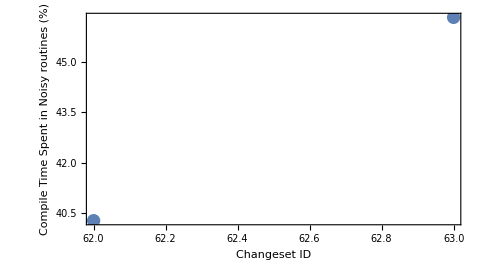
DTraceFcall-noisy-darwin-EN
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
DTraceFcall-noisy-darwin-EN
-Graphics--Graphics--Graphics-

Noisy Compiler on helloWorld.n
Function | % of Runtime
noisyParserSemanticError | 0.119374
noisyRunPasses | 0.12989
noisySymbolTableCloseScope | 0.220345
noisySymbolTableAllocScope | 0.285875
noisySymbolTableSymbolForIdentifier | 0.511186
noisyTimestampsInit | 0.534554
noisyLexPut | 2.43607
noisyLexGet | 2.66966
noisyLexAllocateToken | 2.83723
noisyLexAllocateSourceInfo | 2.90431
noisyConsolePrintBuffers | 3.48648
genNoisyIrNode | 5.21088
flexfree | 5.71603
noisyInit | 6.75515
noisyLexPeek | 12.5239
Other | 53.6591

```mathematica
latestFile = "/Volumes/doos/Noisy-lang-compiler-hg/statistics/latest.txt";

Style["Changeset:    "<>Import["!grep 'changeset:' "<>latestFile<>" | awk '{print $2}'", "List"], Large, Bold, Background->LightBlue]

Column[Parallelize[{
plotChangeSet[latestFile,"DTraceFcall-noisy-darwin-EN"],
plotForDirectory["/Volumes/doos/Noisy-lang-compiler-hg/statistics","DTraceFcall-noisy-darwin-EN"]
}]]

Column[{Style["Noisy Compiler on helloWorld.n", Bold, Large, FontFamily->"Helvetica Neue",Orange], TableForm[dtraceStatsForFile["/Volumes/doos/Noisy-lang-compiler-hg/statistics/latest.txt", "DTraceFcall-noisy-darwin-EN"],TableHeadings->{None,{Style["Function", Bold, FontFamily->"Helvetica Neue"],Style["% of Runtime", Bold, FontFamily->"Helvetica Neue"]}}]}]
```